## Matrix Element calculation (including time evolution)

```mathematica
L =3*10^-7; Lstep =1*10^-8; LN = 2*L/Lstep + 1;nmax = 15; τ = 27.102 10^-9;c = 2.997 10^8;hbar = 1.0545718×10^-34;m = 132.90 * 1.660539 10^-27 ; 
Uprop[x_,xt_,t_,ωt_]:= ((m ωt)/(2 Pi ⅈ hbar Sin[ ωt  t]))^(1/2)Exp[(ⅈ m ωt)/(2 hbar Sin[ωt t])((x^2+xt^2) Cos[ωt t ] - 2 x xt)]
deltak = 2 Pi/(455 10^-9)//N
ψ[x_, n_, ω_]:= 1/Sqrt[2^n n!]((m ω)/(Pi hbar))^(1/4)Exp[(-m ω x^2)/(2 hbar)]HermiteH[n, Sqrt[(m ω)/hbar]x]*Exp[-ⅈ  deltak x]
ψf[x_, n_, ω_]:= 1/Sqrt[2^n n!]((m ω)/(Pi hbar))^(1/4)Exp[(-m ω x^2)/(2 hbar)]HermiteH[n, Sqrt[(m ω)/hbar]x]
```

```mathematica
L =0.4*10^-7; Lstep =0.1*10^-8; LN = 2*L/Lstep + 1;
```

```mathematica
UPn[ω_, ωt_,n_, nt_, t_] := Lstep^2 *Sum[ψ[xt, nt, ωt]*ψ[x, n, ω]*Uprop[x,xt,t,ωt],{x,-L,L,Lstep}, {xt,-L,L,Lstep}]
```

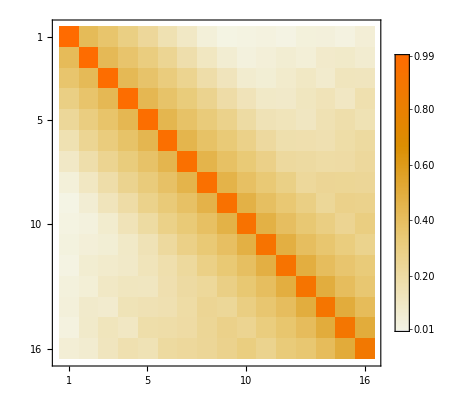

```mathematica
Monitor[uma = Table[Abs[UPn[10^7,10^7,n,nt,200*10^-9]]^2,{n,0,nmax},{nt,0,nmax}];,{n,nt}]
MatrixPlot[uma, PlotLegends -> True]
```

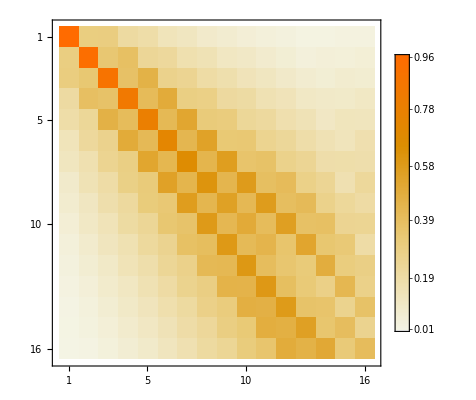

```mathematica
Monitor[uma = Table[Abs[UPn[10^7,0.7*10^7,n,nt,200*10^-9]]^2,{n,0,nmax},{nt,0,nmax}];,{n,nt}]
MatrixPlot[uma, PlotLegends -> True]
```

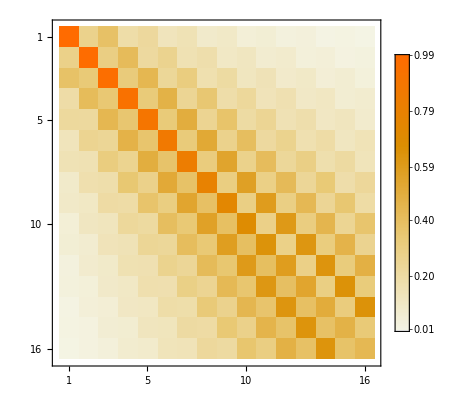

```mathematica
Monitor[uma = Table[Abs[UPn[10^7,1.3*10^7,n,nt,200*10^-9]]^2,{n,0,nmax},{nt,0,nmax}];,{n,nt}]
MatrixPlot[uma, PlotLegends -> True]
```

## Calculate matrix elements for all segments

```mathematica
(*from LambDickeParams_Singe.py @532nm and @10**7 lattice beam intensity *)
(*levels=["6s 2 S 1/2","7p 2 P ?3/2","7s 2 S 1/2","6p 2 P ?1/2","6p 2 P ?3/2","5d 2 D 3/2","5d 2 D 5/2"]*)
(*decays=[l21,l23,l35,l41,l64,l51,l65,l75,l27,l26,l34]*)
omegas = {93404.36151476773,58312.21388517295,52564.18722654877,96487.56959133178,149378.74074871602,114323.656390064,134446.8575802304};
etas = {0.697646827167697,0.14448683087878345,0.17095247621856766,0.35533728030290285,0.10383570605450117,0.3729352538139725,0.06952852571696208,0.07198024772090308,0.19467123685222815,0.21390857630773225,0.23003214721947357};
l21=455.5*10^-9;
l23=2931.8*10^-9;
l35=1469.9*10^-9;
l41=894.3*10^-9;
l64=3011.1*10^-9;
l51=852.1*10^-9;
l65=3614.1*10^-9;
l75=3491*10^-9;
l27=1360.6*10^-9;
l26=1342.8*10^-9;
l34=1359.2*10^-9;
decays={l21,l23,l35,l41,l64,l51,l65,l75,l27,l26,l34};
g23=4.05*10^6;
g34=6.23*10^6;
g35=11.4*10^6;
g41=28.6*10^6;
g26=0.13*10^6;
g27=1.10*10^6;
g75=0.78*10^6;
g65=0.11*10^6;
g51=32.8*10^6;
g64=0.91*10^6;
g21=1.84*10^6;
gammas={g21,g23,g35,g41,g64,g51,g65,g75,g27,g26,g34};
omega[n_]:= omegas[[n]]
eta[n_]:= etas[[n]]
```